```mathematica
ClearAll["Global`*"];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]];
plot2Doption=Append[{PlotRange->All,PlotStyle->Red,Filling->Axis,GridLines->All,Joined->False},plot2Doption];
```

Available:plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
getOmegaFromKandDepth
getTFromLandDepth

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"ultrasonic_sensor_data.csv"}]];
listORG=data[[100;;]][[;;,2]];
listTMP=data[[100;;]][[;;,2]];
list=listTMP;
max=5
Do[listTMP[[i]]=0.5listTMP[[i-1]]+0.5listTMP[[i]],{i,max+1,Length[listTMP]-max}]
Do[list[[i]]=Mean[Table[listTMP[[j+i]],{j,-max,max,1}]],{i,max+1,Length[listORG]-max}]
casename="ultrasonic_sensor";
```

5

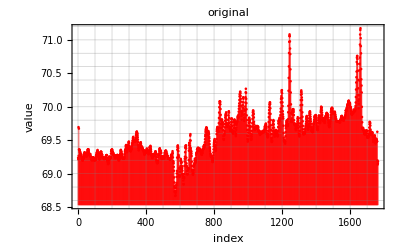

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_original_ultrasonic_sensor.png

```mathematica
(*list=Table[Cos[2π/n*i]*Cos[5π/n*i],{i,0,n-1,1}];*)
fig=ListPlot[list,PlotLabel->"original",FrameLabel->{"index","value"},GridLines->All, Joined->False,Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_original_"<>casename<>".png"}],fig]
```

```mathematica
Column[N@list,Frame->All];
num=30
(*list=Flatten@{Table[1,{i,1,num}],Table[2,{i,1,num}]}*)
(*list=Table[Cos[2π*i/num],{i,0,num-1}]*)

Grid[#,Frame->All]&@
{{"組み込みDFT","ユーザー定義DFT"},
{Column[Fourier[list,FourierParameters->{-1,-1}],Frame->All],
Column[cn=Table[MyFourier[list,n],{n,0,Length[list]-1}],Frame->All]}}
```

30

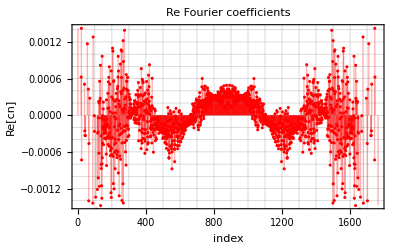

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_cn_ultrasonic_sensor.png

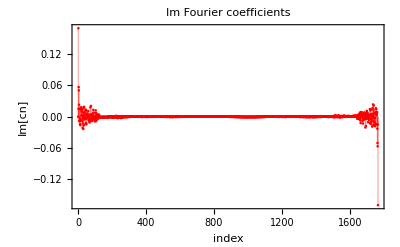

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Im_cn_ultrasonic_sensor.png

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_ReIm_cn_ultrasonic_sensor.png

```mathematica
figRe=ListPlot[Re[cn],PlotLabel->"Re Fourier coefficients",FrameLabel->{"index","Re[cn]"},PlotRange->{{1,All},Automatic},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_cn_"<>casename<>".png"}],figRe]

figIm=ListPlot[Im[cn],PlotLabel->"Im Fourier coefficients",FrameLabel->{"index","Im[cn]"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Im_cn_"<>casename<>".png"}],figIm]

Export[FileNameJoin[{NotebookDirectory[],"./sample_ReIm_cn_"<>casename<>".png"}],Row[{figRe,figIm}]]
```

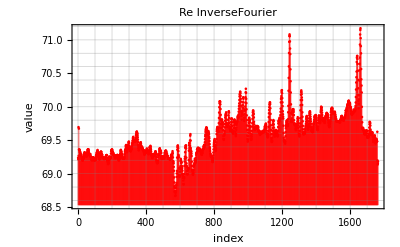

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_inv_ultrasonic_sensor.png

```mathematica
len=Length[list];

Grid[#,Frame->All]&@{{"InverseDFT","User defined InverseDFT"},
{Column[inv=InverseFourier[cn,FourierParameters->{-1,-1}],Frame->All],
Column[Table[MyInverseFourier[cn,n],{n,0,Length[list]-1,1}],Frame->All]}};

(*■*)fig=ListPlot[Re[inv],PlotLabel->"Re InverseFourier",FrameLabel->{"index","value"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_inv_"<>casename<>".png"}],fig]
```

```mathematica
(*n-1->-1*)
(*n-2->-2*)
Floor[Length[cn]-1]
shift=If[EvenQ[(Length[cn]-1)/2],{(Length[cn]-1)/2,(Length[cn]-1)/2},{(Length[cn]-1+1)/2,(Length[cn]-1-1)/2}]
Do[Cn[i]=cn[[i+1]],{i,0,shift[[1]]}]
Do[Cn[-i]=cn[[Length[cn]+1-i]],{i,1,shift[[2]]}]
```

1763

{882,881}

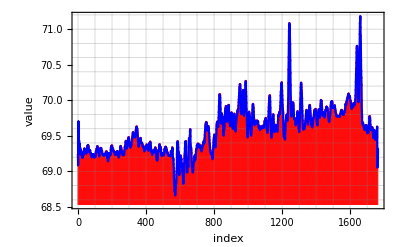

```mathematica
f[t_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-shift[[2]],shift[[1]],1}]];
fig=Show[
ListPlot[ParallelTable[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[ParallelTable[{t,Re[f[t]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"./sample_interpolation_"<>casename<>".png"}],fig]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_interpolation_ultrasonic_sensor.png

```mathematica
f[t_,expandmax_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-expandmax,expandmax,1}]];
anim=Manipulate[
Show[
ListPlot[Table[{i-1,listORG[[i]]},{i,1,Length[listORG],1}],FrameLabel->{"index","value"},PlotStyle->Blue,Evaluate[plot2Doption]],
ListPlot[Table[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[Table[{t,Re[f[t,expandmax]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
,PlotLabel->expandmax
],{expandmax,1,Min[shift],1}]
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"./sample_convergence_"<>casename<>".gif"}],anim]*)
```